```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;
```

```mathematica
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/4000))-1)* (v0+v1/(1+M[x]/4000))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/4000))* (v0+v1/(1+M[x]/4000))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,700}]
```

{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

```mathematica
s2=NDSolve[{SS'[x]==(2 *(P0+P1/(1+MM[x]/4000))-1)* (v0+v1/(1+MM[x]/4000))*SS[x],MM'[x]==2 *(1-P0-P1/(1+MM[x]/4000))* (v0+v1/(1+MM[x]/4000))* SS[x]-d*MM[x],SS[380]==0.9*1099.9,MM[380]==0.9*21333.5},{SS,MM},{x,380,700}]
```

{{SS→InterpolatingFunction[…],MM→InterpolatingFunction[…]}}

```mathematica
s3=NDSolve[{SSS'[x]==(2 *(P0+P1/(1+MMM[x]/4000))-1)* (v0+v1/(1+MMM[x]/4000))*SSS[x],MMM'[x]==2 *(1-P0-P1/(1+MMM[x]/4000))* (v0+v1/(1+MMM[x]/4000))* SSS[x]-d*MMM[x],SSS[380]==0.8*1099.9,MMM[380]==0.8*21333.5},{SSS,MMM},{x,380,700}]
```

{{SSS→InterpolatingFunction[…],MMM→InterpolatingFunction[…]}}

```mathematica
s4=NDSolve[{SSSS'[x]==(2 *(P0+P1/(1+MMMM[x]/4000))-1)* (v0+v1/(1+MMMM[x]/4000))*SSSS[x],MMMM'[x]==2 *(1-P0-P1/(1+MMMM[x]/4000))* (v0+v1/(1+MMMM[x]/4000))* SSSS[x]-d*MMMM[x],SSSS[380]==0.7*1099.9,MMMM[380]==0.7*21333.5},{SSSS,MMMM},{x,380,700}]
```

{{SSSS→InterpolatingFunction[…],MMMM→InterpolatingFunction[…]}}

```mathematica
{{SSSS->InterpolatingFunction[…],MMMM->InterpolatingFunction[…]}}
s5=NDSolve[{SSSSS'[x]==(2 *(P0+P1/(1+MMMMM[x]/4000))-1)* (v0+v1/(1+MMMMM[x]/4000))*SSSSS[x],MMMMM'[x]==2 *(1-P0-P1/(1+MMMMM[x]/4000))* (v0+v1/(1+MMMMM[x]/4000))* SSSSS[x]-d*MMMMM[x],SSSSS[380]==0.9*1099.9,MMMMM[380]==0.8*21333.5},{SSSSS,MMMMM},{x,380,700}]
s6=NDSolve[{SSSSSS'[x]==(2 *(P0+P1/(1+MMMMMM[x]/4000))-1)* (v0+v1/(1+MMMMMM[x]/4000))*SSSSSS[x],MMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMM[x]/4000))* (v0+v1/(1+MMMMMM[x]/4000))* SSSSSS[x]-d*MMMMMM[x],SSSSSS[380]==0.8*1099.9,MMMMMM[380]==0.9*21333.5},{SSSSSS,MMMMMM},{x,380,700}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s7=NDSolve[{SSSSSSS'[x]==(2 *(P0+P1/(1+MMMMMMM[x]/4000))-1)* (v0+v1/(1+MMMMMMM[x]/4000))*SSSSSSS[x],MMMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMMM[x]/4000))* (v0+v1/(1+MMMMMMM[x]/4000))* SSSSSSS[x]-d*MMMMMMM[x],SSSSSSS[380]==0.9*1099.9,MMMMMMM[380]==0.7*21333.5},{SSSSSSS,MMMMMMM},{x,380,700}]
s8=NDSolve[{SSSSSSSS'[x]==(2 *(P0+P1/(1+MMMMMMMM[x]/4000))-1)* (v0+v1/(1+MMMMMMMM[x]/4000))*SSSSSSSS[x],MMMMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMMMM[x]/4000))* (v0+v1/(1+MMMMMMMM[x]/4000))* SSSSSSSS[x]-d*MMMMMMMM[x],SSSSSSSS[380]==0.7*1099.9,MMMMMMMM[380]==0.9*21333.5},{SSSSSSSS,MMMMMMMM},{x,380,700}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s9=NDSolve[{SSSSSSSSS'[x]==(2 *(P0+P1/(1+MMMMMMMMM[x]/4000))-1)* (v0+v1/(1+MMMMMMMMM[x]/4000))*SSSSSSSSS[x],MMMMMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMMMMM[x]/4000))* (v0+v1/(1+MMMMMMMMM[x]/4000))* SSSSSSSSS[x]-d*MMMMMMMMM[x],SSSSSSSSS[380]==0.2*1099.9,MMMMMMMMM[380]==0.7*21333.5},{SSSSSSSSS,MMMMMMMMM},{x,380,700}]
s10=NDSolve[{SSSSSSSSSS'[x]==(2 *(P0+P1/(1+MMMMMMMMMM[x]/4000))-1)* (v0+v1/(1+MMMMMMMMMM[x]/4000))*SSSSSSSSSS[x],MMMMMMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMMMMMM[x]/4000))* (v0+v1/(1+MMMMMMMMMM[x]/4000))* SSSSSSSSSS[x]-d*MMMMMMMMMM[x],SSSSSSSSSS[380]==0.7*1099.9,MMMMMMMMMM[380]==0.2*21333.5},{SSSSSSSSSS,MMMMMMMMMM},{x,380,700}]
```

{{SSSS→InterpolatingFunction[…],MMMM→InterpolatingFunction[…]}}

{{SSSSS→InterpolatingFunction[…],MMMMM→InterpolatingFunction[…]}}

{{SSSSSS→InterpolatingFunction[…],MMMMMM→InterpolatingFunction[…]}}

{{SSSSSSS→InterpolatingFunction[…],MMMMMMM→InterpolatingFunction[…]}}

{{SSSSSSSS→InterpolatingFunction[…],MMMMMMMM→InterpolatingFunction[…]}}

{{SSSSSSSSS→InterpolatingFunction[…],MMMMMMMMM→InterpolatingFunction[…]}}

{{SSSSSSSSSS→InterpolatingFunction[…],MMMMMMMMMM→InterpolatingFunction[…]}}

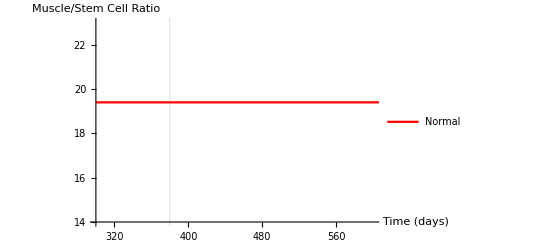

```mathematica
p1=Plot[Evaluate[(M[x]/.s1)/(S[x]/.s1)],{x,300,700},AxesLabel->{"Time (days)","Muscle/Stem Cell Ratio"},     GridLines->{{380},{}}, PlotStyle->Red,PlotRange->{{300,600},{14,23}},PlotLegends->{"Normal"}]
```

```mathematica
p2=Plot[Evaluate[(MM[x]/.s2)/(SS[x]/.s2)],{x,380,700},PlotRange->{{0,700},{0,0.1}},AxesLabel->{"Time (days)","Mass (grams)"},PlotLabel->"Stem Mass",PlotStyle->Blue,PlotLegends->{"10% loss in muscle and sem cells"}]
```

-Graphics-

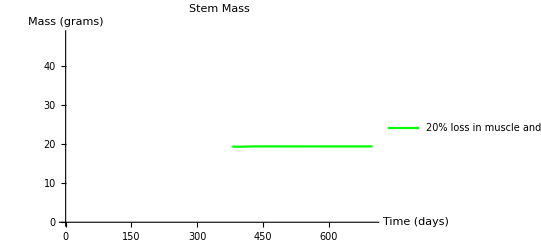

```mathematica
p3=Plot[Evaluate[(MMM[x]/.s3)/(SSS[x]/.s3)],{x,380,700},PlotRange->{{0,700},{0,48}},AxesLabel->{"Time (days)","Mass (grams)"},PlotLabel->"Stem Mass",PlotStyle->Green,PlotLegends->{"20% loss in muscle and sem cells"}]
```

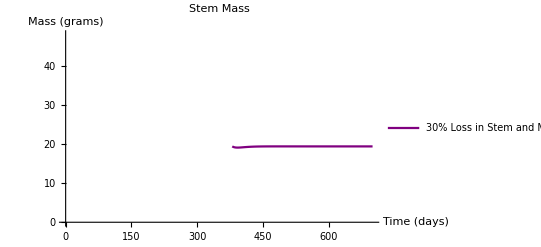

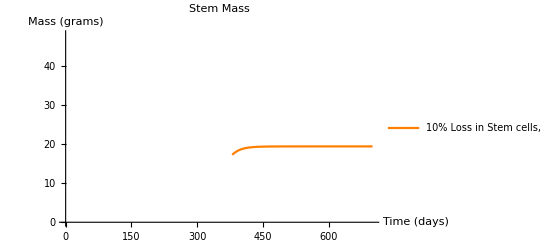

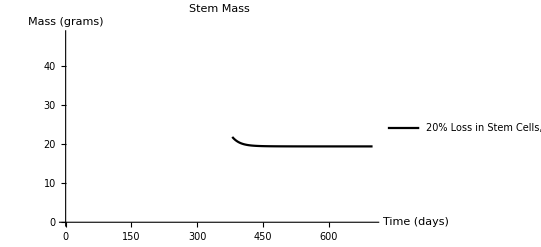

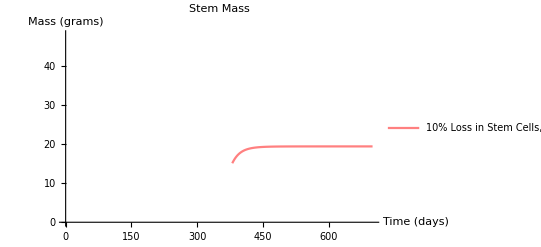

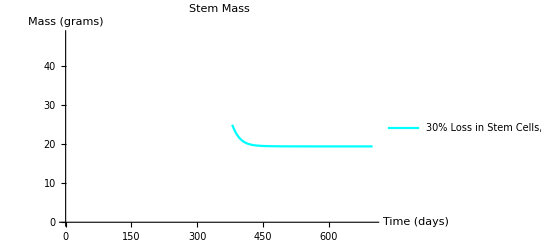

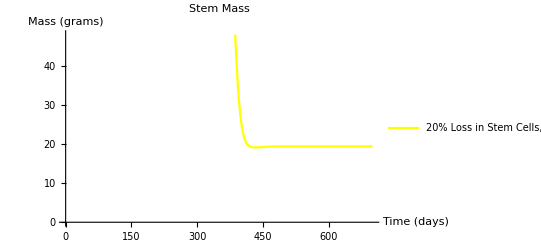

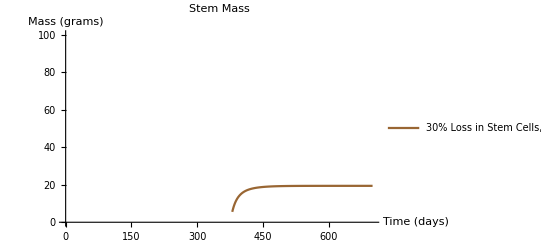

```mathematica
p4=Plot[Evaluate[(MMMM[x]/.s4)/(SSSS[x]/.s4)],{x,380,700},PlotRange->{{0,700},{0,48}},AxesLabel->{"Time (days)","Mass (grams)"},PlotLabel->"Stem Mass",PlotStyle->Purple,PlotLegends->{"30% Loss in Stem and Muscle Cells"}]
p5=Plot[Evaluate[(MMMMM[x]/.s5)/(SSSSS[x]/.s5)],{x,380,700},PlotRange->{{0,700},{0,48}},AxesLabel->{"Time (days)","Mass (grams)"},PlotLabel->"Stem Mass",PlotStyle->Orange,PlotLegends->{"10% Loss in Stem cells, 20% Loss in Muscle Cells"}]
p6=Plot[Evaluate[(MMMMMM[x]/.s6)/(SSSSSS[x]/.s6)],{x,380,700},PlotRange->{{0,700},{0,48}},AxesLabel->{"Time (days)","Mass (grams)"},PlotLabel->"Stem Mass",PlotStyle->Black,PlotLegends->{"20% Loss in Stem Cells, 10% Loss in Muscle Cells"}]
p7=Plot[Evaluate[(MMMMMMM[x]/.s7)/(SSSSSSS[x]/.s7)],{x,380,700},PlotRange->{{0,700},{0,48}},AxesLabel->{"Time (days)","Mass (grams)"},PlotLabel->"Stem Mass",PlotStyle->Pink,PlotLegends->{"10% Loss in Stem Cells, 30% Loss in Muscle Cells"}]
p8=Plot[Evaluate[(MMMMMMMM[x]/.s8)/(SSSSSSSS[x]/.s8)],{x,380,700},PlotRange->{{0,700},{0,48}},AxesLabel->{"Time (days)","Mass (grams)"},PlotLabel->"Stem Mass",PlotStyle->Cyan,PlotLegends->{"30% Loss in Stem Cells, 10% Loss in Muscle Cells"}]
p9=Plot[Evaluate[(MMMMMMMMM[x]/.s9)/(SSSSSSSSS[x]/.s9)],{x,380,700},PlotRange->{{0,700},{0,48}},AxesLabel->{"Time (days)","Mass (grams)"},PlotLabel->"Stem Mass",PlotStyle->Yellow,PlotLegends->{"20% Loss in Stem Cells, 30% Loss in Muscle Cells"}]
p10=Plot[Evaluate[(MMMMMMMMMM[x]/.s10)/(SSSSSSSSSS[x]/.s10)],{x,380,700},PlotRange->{{0,700},{0,100}},AxesLabel->{"Time (days)","Mass (grams)"},PlotLabel->"Stem Mass",PlotStyle->Brown,PlotLegends->{"30% Loss in Stem Cells, 20% Loss in Muscle Cells"}]
```

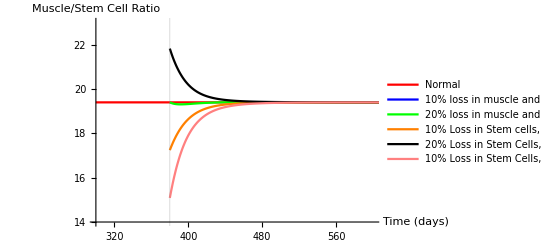

```mathematica
Show[p1,p5,p6]
```

```mathematica
(*For[x=100,x<501,x+=1,
stem={0.002*S[x]}/.s1;
muscle={0.002*M[x]}/.s1;
muscle2={0.002*MM[x]}/.s2;
muscle3={0.002*MMM[x]}/.s3;
muscle4={0.002*MMMM[x]}/.s4;
dif2=muscle-muscle2;
dif3=muscle-muscle3;
dif4=muscle-muscle4;
(*stem1={0.002*S[x]}/.s1;muscle1={0.002*M[x]}/.s1;
stem2={0.002*SS[x]}/.s2;muscle2={0.002*MM[x]}/.s2;
stem3={0.002*SSS[x]}/.s3;muscle3={0.002*MMM[x]}/.s3;
stem4={0.002*SSSS[x]}/.s4;muscle4={0.002*MMMM[x]}/.s4;
ratio1=muscle1/stem1;ratio2=muscle2/stem2;ratio3=muscle3/stem3;ratio4=muscle4/stem4;*)


Print[x,"  ",dif2,"      ",Abs[dif2-0.1],"   ",dif3,"    ",Abs[dif3-0.1],"   ",dif4,"   ",Abs[dif4-0.1](*ratio1,"   ",ratio2,"   ",ratio3,"   ",ratio4*)]]*)
```

```mathematica
(*For[x=380,x≤380,x+=1,
stem={S[x]}/.s1;
muscle={M[x]}/.s1;


Print[x,"  ",stem,"  ",muscle]]*)
```